```mathematica
CellularAutomaton[30,{1,1, 0},2]
```

{{1,1,0},{1,0,0},{1,1,1}}

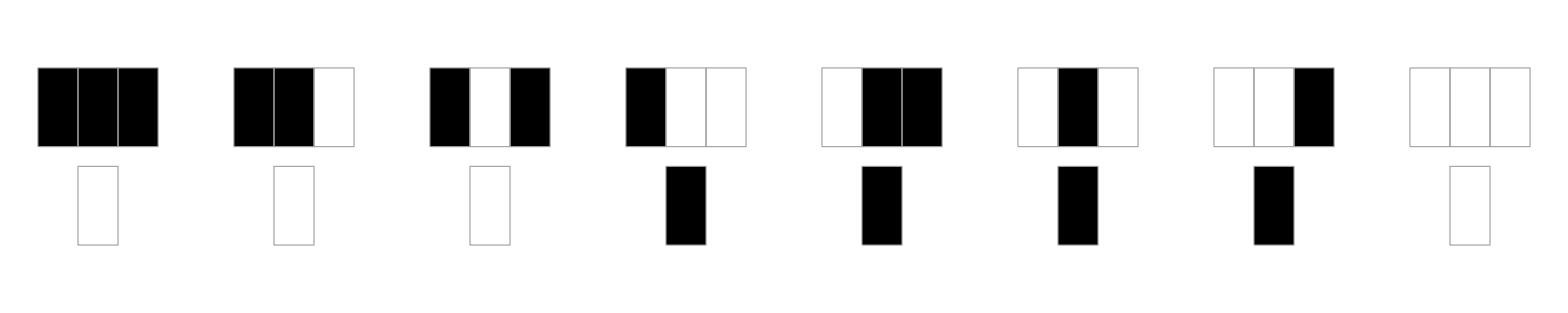

```mathematica
RulePlot[CellularAutomaton[30]]
```

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},50]]
```

-Graphics-

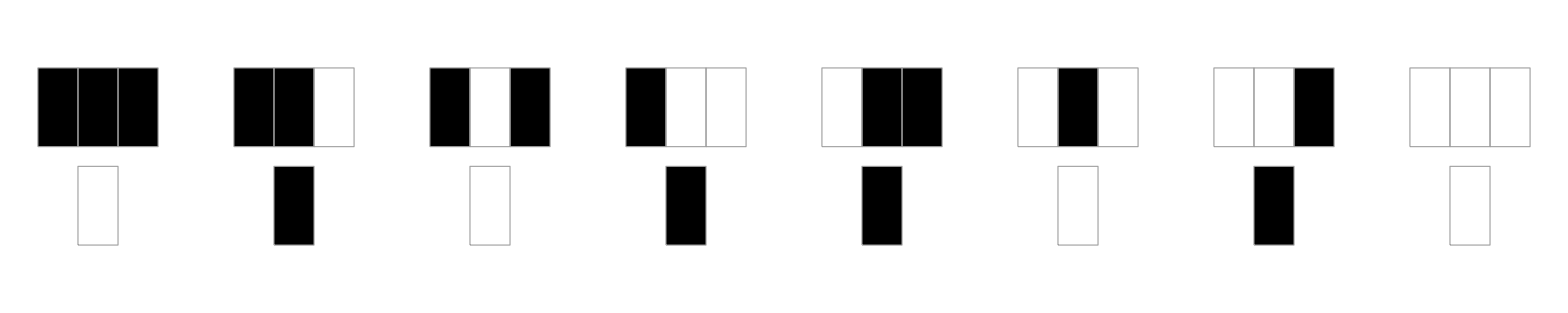

```mathematica
RulePlot[CellularAutomaton[90]]
```

```mathematica
ArrayPlot[CellularAutomaton[90,{{1},0},1000]]
```

-Graphics-

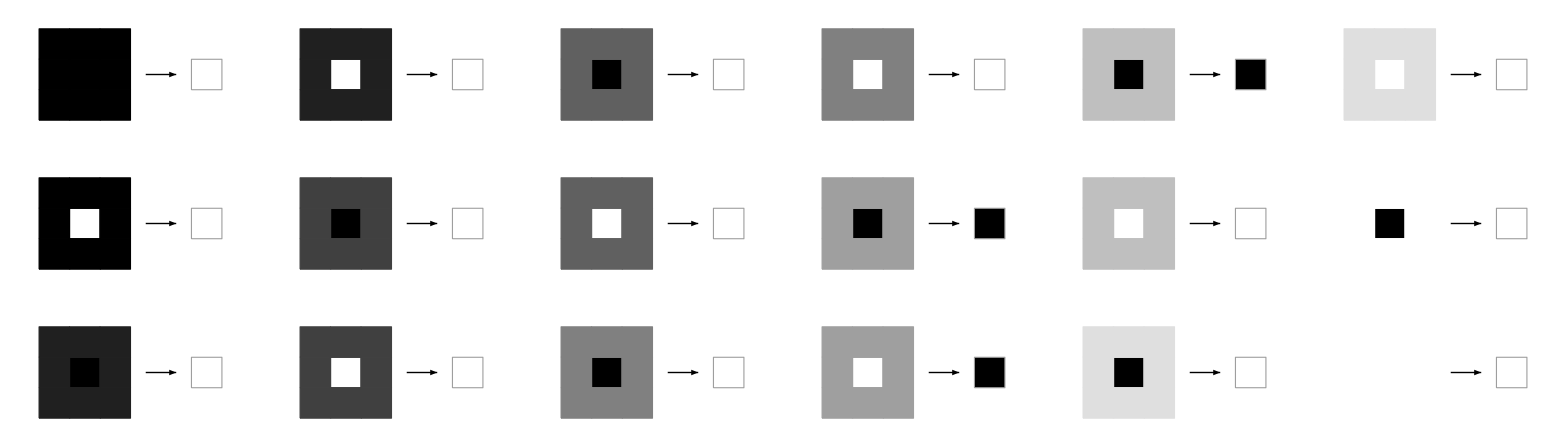

```mathematica
RulePlot[CellularAutomaton["GameOfLife"]]
```

```mathematica
board=RandomInteger[1,{100,100}];
Dynamic[ArrayPlot[board=Last[CellularAutomaton["GameOfLife",board,{{0,1}}]]]]
```

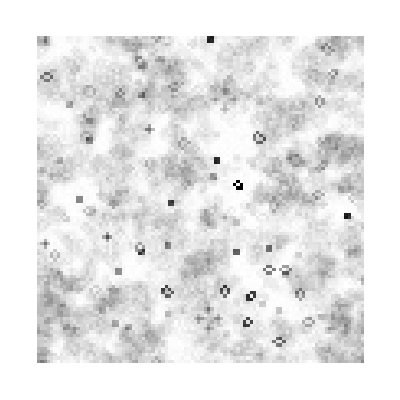

```mathematica
ArrayPlot[Mean[CellularAutomaton["GameOfLife",RandomInteger[1,{100,100}],100]]]
```

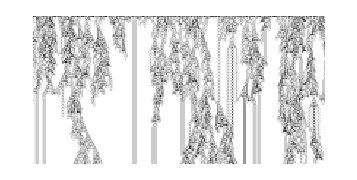

```mathematica
ArrayPlot[Mean/@CellularAutomaton["GameOfLife",RandomInteger[1,{10,200}],100]]
```

```mathematica
ArrayPlot[#,ImageSize->40,Mesh->True]&/@CellularAutomaton["GameOfLife",{{{0,1,0},{0,0,1},{1,1,1}},0},8]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics3D[Cuboid/@Position[CellularAutomaton[{14,{2,1},{1,1}},{{{1}},0},10],1],ViewVertical->{-1,0,0}]
```

```mathematica
Graphics3D[Cuboid/@Position[#,1],ImageSize->Tiny]&/@CellularAutomaton[{14,{2,1},{1,1,1}},{{{{1}}},0},10]
```